## ВВЕДЕНИЕ В ВЕЙВЛЕТ - ПРЕОБРАЗОВАНИЕ

Оригинал: https://cseweb.ucsd.edu/~baden/Doc/wavelets/polikar_wavelets.pdf
Перевод: http://www.autex.spb.su/download/wavelet/books/tutorial.pdf

### Преобразование Фурье

Математические преобразования применяются к сигналу для того, чтобы получить о нем какую - то дополнительную информацию, недоступную в исходном виде.В дальнейшем изложении сигнал во временной области будет называться «исходным», а преобразованный сигнал - трансформантой.Среди многих известных преобразований сигналов наиболее популярным является преобразование Фурье.
Большинство сигналов, встречающихся на практике, представлены во временной области, то есть сигнал есть функция времени.Таким образом, при отображении сигнала на графике одной из координат (независимой) является ось времени, а другой координатой (зависимой)–ось амплитуд.Таким образом мы получаем амплитудно - временное представление сигнала.Для большинства приложений обработки сигнала это представление не является наилучшим.Во многих случаях наиболее значимая информация скрыта в частотной области сигнала.Частотный спектр есть совокупность частотных (спектральных) компонент, он отображает наличие тех или иных частот в сигнале.
Как известно, частота измеряется в Герцах[Гц], или в числе периодов в секунду.На рисунке ниже для примера представлены три синусоиды : 3 Гц, 10 Гц и 50 Гц.Сравните их.

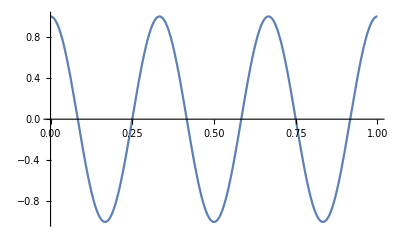

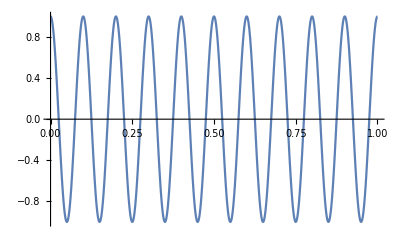

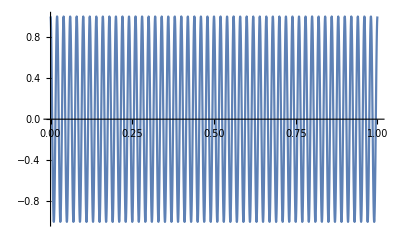

```mathematica
s[f_,t_]:= Cos[ 2 Pi f *t] 
Plot[s[3,t],{t,0,1}]
Plot[s[10,t],{t,0,1}]
Plot[s[50,t],{t,0,1}]
```

А каким же образом мы измеряем, находим частоту сигнала?
Способ называется ПРЕОБРАЗОВАНИЕ ФУРЬЕ (ПФ).В результате ПФ сигнала, заданного во временной области, мы получаем его спектральное представление.Вместо значений времени на оси абсцисс графика сигнала будет теперь отложены значения частоты, а ось ординат будет отображать амплитуду той или иной частоты в сигнале.Частотная ось начинается с нуля и простирается до бесконечности.Например, если взять ПФ сигнала электрического тока в наших розетках, то мы получим единственный импульс на частоте 50 Гц, а остальные значения амплитуд будут равны нулю.Реальные сигналы обычно состоят из множества частот и редко имеют подобные простые графики. Ниже показано ПФ синусоиды с частотой 50 Гц :

```mathematica
ft= FourierTransform[s[50,t],t,2Pi f]
```

DiracDelta[-50+f]/(2 √(2 π))+DiracDelta[50+f]/(2 √(2 π))

Внимание! Рассмотренные решения являются непрерывными. Теперь же рассмотрим дискретный вариант.

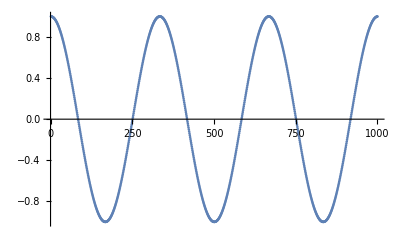

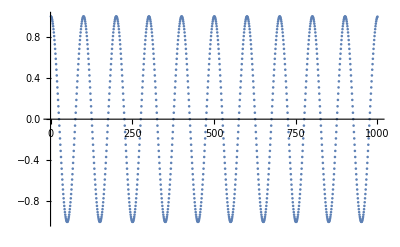

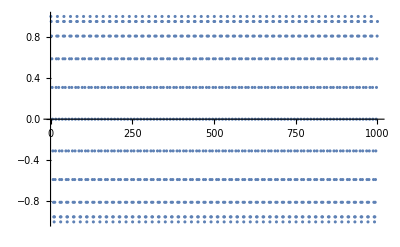

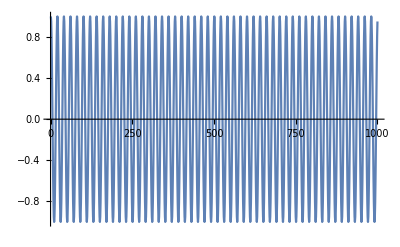

```mathematica
T=1 ;(* время в секундах *)
Δ=1000; (* колво отсчетов внутри T *)
sd[f_,T_,Δ_]:=Cos[ 2 Pi f T/Δ *t]
sd3=Table[   sd[3,T,Δ], {t,0,Δ-1}];
sd10=Table[   sd[10,T,Δ], {t,0,Δ-1}];
sd50=Table[   sd[50,T,Δ], {t,0,Δ-1}];

ListPlot[sd3]
ListPlot[sd10]
ListPlot[sd50]
ListLinePlot[sd50]
```

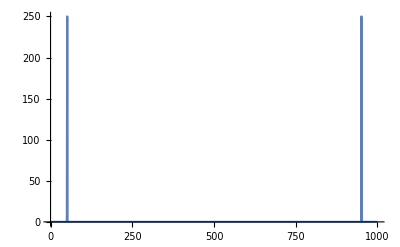

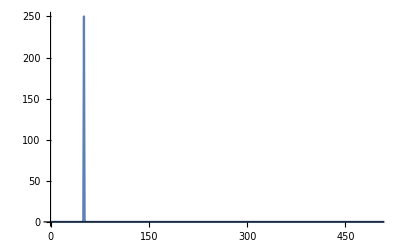

```mathematica
ft= Abs[Fourier[sd50]]^2;  (*мощность спектра*)
ListLinePlot[ft,PlotRange->All]
ListLinePlot[ft,PlotRange->{{0,Δ/2 -1},All}]
```

```mathematica
Max[ft];
max=Ordering[ ft[[;;Δ/2]],-1]//First;
f0=(max-1)/T
```

50

Кроме ПФ существует и много других часто применяемых преобразований сигнала. Примерами являются преобразование Гильберта, оконное ПФ, распределение Вигнера, преобразование Уолша, вейвлет-преобразование и многие другие. Для каждого преобразования можно указать наиболее подходящую область применения, достоинства и недостатки, и вейвлет- преобразование (ВП) не является в этом смысле исключением.
Для лучшего понимания потребности в ВП рассмотрим подробнее ПФ. ПФ (также, как и ВП) является обратимым образованием, то есть из его коэффициентов посредством обратного преобразования может быть получен исходный сигнал. Однако только одно из представлений доступно для нас в каждый момент времени: частотную информацию нельзя извлечь из временной, а временную - из частотной. Возникает естественный вопрос: возможно ли получить совместное частотно-временное представление сигнала?
Как будет показано, ответ зависит от конкретного приложения и от природы сигнала. Напомним, что ПФ дает частотную информацию, содержащуюся в сигнале, то есть говорит нам о том, каково содержание каждой частоты в сигнале. Однако в какой момент времени возникла та или иная частота, когда она закончилась - на эти вопросы ответ получить не удастся. Впрочем, эта информация и не требуется, если сигнал – стационарный.
Давайте поподробнее обсудим концепцию стационарности, так как она несомненно одна из наиболее важных при анализе сигнала. Стационарными называются сигналы, частотное наполнение которых не меняется во времени. Поэтому при частотном анализе таких сигналов и не требуется временная информация - все частоты присутствуют в сигнале на протяжении всего времени.
Например, следующий сигнал 
					x(t) = cos(2π 10t) + cos(2π 25t) + cos(2π 50t) + cos(2π100t)
является стационарным, так как содержащиеся в нем частоты 10, 25, 50 и 100 Гц не меняются во времени. Этот сигнал изображен ниже:

10

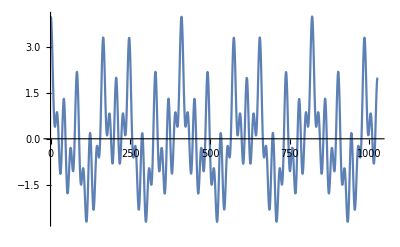

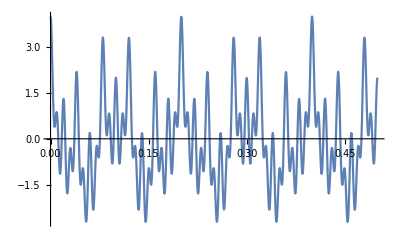

```mathematica
T=0.5 ;(* время в секундах *)
n=10
Δ=2^n; (* колво отсчетов внутри T *)
st=sd[10,T,Δ]+sd[25,T,Δ]+sd[50,T,Δ]+sd[100,T,Δ];
xt=Table[st,{t,0,Δ}];
ListLinePlot[xt]
ListLinePlot[xt,DataRange->{0,T}]
```

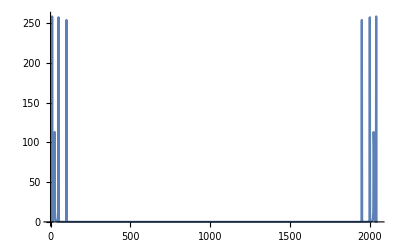

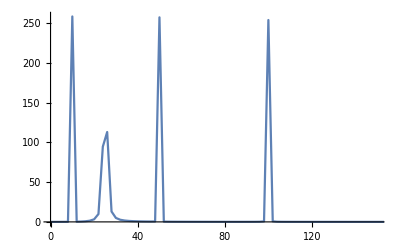

```mathematica
ft= Abs[Fourier[xt]]^2;  (*мощность спектра*)
ListLinePlot[ft,PlotRange->All,DataRange->{0,Δ/T-1}]
ListLinePlot[ft,PlotRange->{{0,150},All},DataRange->{0,Δ/T-1}]
```

```mathematica
md=MaxDetect[ft[[;;Δ/2]]];
max=Position[md,1]//Flatten
f0=(#-1)/T &/@max
```

{6,14,26,51}

{10.,26.,50.,100.}

Сигнал, изображенный в следующем примере, нестационарный. Его частота непрерывно изменяется во времени. Такой сигнал называется сигналом с линейной частотной модуляцией (ЛЧМ). В зарубежной литературе он называется «chirp»-сигналом.

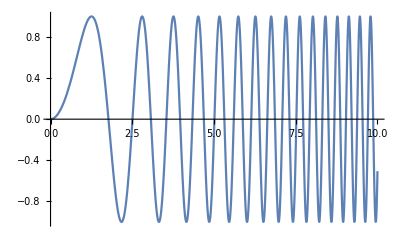

```mathematica
Plot[Sin[t*t],{t,0,10}]
```

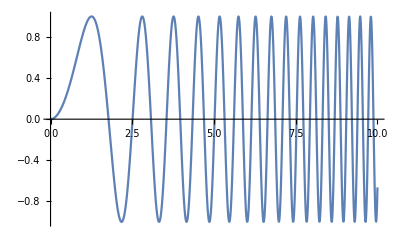

```mathematica
T=10;(* время в секундах *)
n=10;
Δ=2^n; (* колво отсчетов внутри T *)
st=Sin[t  (T/Δ)   *t  (T/Δ)];
xt=Table[st,{t,0,Δ-1}];
ListLinePlot[xt,DataRange->{0,T}]
```

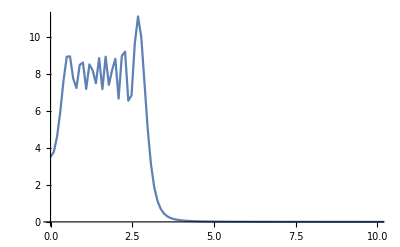

```mathematica
ft= Abs[Fourier[xt]]^2;  (*мощность спектра*)
ListLinePlot[ft,PlotRange->{{0,10},All},DataRange->{0,Δ/T-1}]
```

А вот и проблема для нестационарного сигнала:

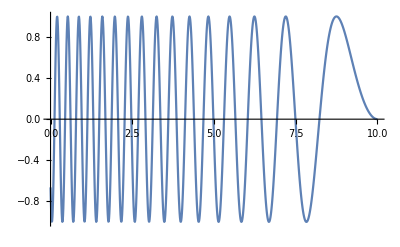

```mathematica
xtr=Reverse[xt];
ListLinePlot[xtr,DataRange->{0,T}]
```

```mathematica
ftr= Abs[Fourier[xtr]]^2;  (*мощность спектра*)
ListLinePlot[ftr,PlotRange->{{0,10},All},DataRange->{0,Δ/T-1}]
```

-Graphics-

Наложим и ... разница отсутствует! А сигналы то разные!

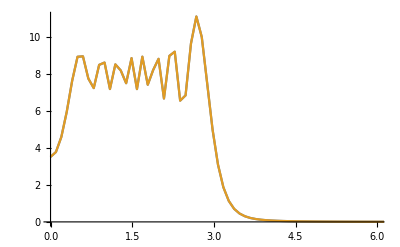

```mathematica
ListLinePlot[{ft,ftr},PlotRange->{{0,6},All},DataRange->{0,Δ/T-1}]
```

ВАЖНО! ПФ может использоваться для анализа нестационарных сигналов, если нас интересует лишь частотная информация, а время существования спектральных составляющих неважно.В противном случае надо искать более подходящий метод анализа.

```mathematica
ShortTimeFourier[xt,Automatic,Automatic]
Spectrogram[%]
```

ShortTimeFourierData[…]

-Graphics-

```mathematica
ShortTimeFourier[xt,256,64]
Spectrogram[%]
```

ShortTimeFourierData[…]

-Graphics-

```mathematica
ShortTimeFourier[xtr,256,64]
Spectrogram[%]
```

ShortTimeFourierData[…]

-Graphics-

Рассмотрим еще один пример. Показан сигнал, состоящий из четырех различных частот, встречающихся на четырех различных интервалах и, следовательно, являющийся нестационарным.В интервале времени от 0 до 300 мс частота сигнала 100 Гц, от 300 до 600 мс–50 Гц, от 600 до 800 мс–25 Гц и на последнем интервале–10 Гц.

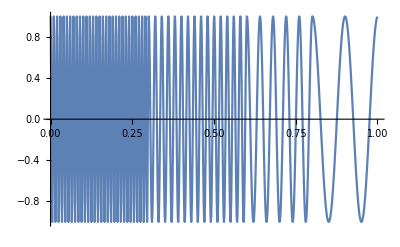

```mathematica
T=1 ;(* время в секундах *)
Δ=1000; (* колво отсчетов внутри T *)
st=Piecewise[{
{sd[100,T,Δ],t<300},
{sd[50,T,Δ],300≤ t<600},
{sd[25,T,Δ],600≤ t<800},
{sd[10,T,Δ],800≤ t}
}];

xt=Table[st,{t,0,Δ-1}];
ListLinePlot[xt,DataRange->{0,T}]
```

```mathematica
ShortTimeFourier[xt]
Spectrogram[%]
```

ShortTimeFourierData[…]

-Graphics-

```mathematica
ShortTimeFourier[xt,300,300]
Spectrogram[%]
```

ShortTimeFourierData[…]

-Graphics-

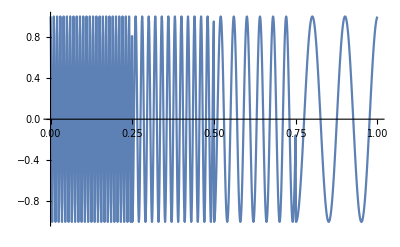

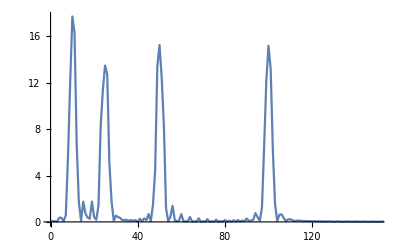

```mathematica
T=1 ;(* время в секундах *)
Δ=1000; (* колво отсчетов внутри T *)
st=Piecewise[{
{sd[100,T,Δ],t<250},
{sd[50,T,Δ],250≤ t<500},
{sd[25,T,Δ],500≤ t<750},
{sd[10,T,Δ],750≤ t}
}];

xt=Table[st,{t,0,Δ-1}];
ListLinePlot[xt,DataRange->{0,T}]
ListLinePlot[ Abs[Fourier[xt]]^2 ,PlotRange->{{0,150},All} ,DataRange->{0,Δ/T-1}]
```

ShortTimeFourierData[…]

-Graphics-

4

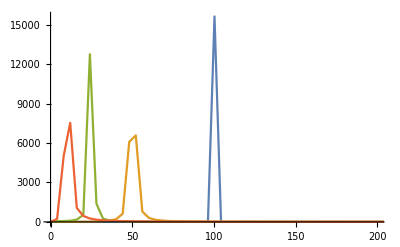

```mathematica
stft=ShortTimeFourier[xt,250,250,DirichletWindow]
Spectrogram[%]
k=Length[stft["Data"]]
ListLinePlot[Abs[stft["Data"][[#]]]^2&/@Range[k],PlotRange->{{0,200},All} ,DataRange->{0,Δ/T-1}]
```

ShortTimeFourierData[…]

-Graphics-

4

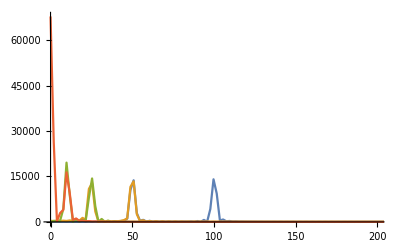

```mathematica
stft=ShortTimeFourier[xt,512,250,DirichletWindow]
Spectrogram[%]
k=Length[stft["Data"]]
ListLinePlot[Abs[stft["Data"][[#]]]^2&/@Range[k],PlotRange->{{0,200},All} ,DataRange->{0,Δ/T-1}]
```

ShortTimeFourierData[…]

-Graphics-

48

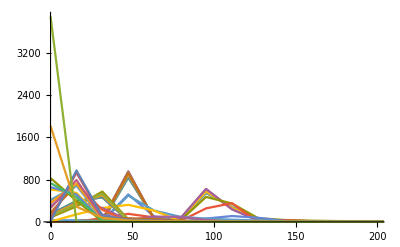

```mathematica
stft=ShortTimeFourier[xt,Automatic,Automatic,DirichletWindow]
Spectrogram[%]
k=Length[stft["Data"]]
ListLinePlot[Abs[stft["Data"][[#]]]^2&/@Range[k],PlotRange->{{0,200},All} ,DataRange->{0,Δ/T-1}]
```

```mathematica
stft=ShortTimeFourier[xt,250,250,DirichletWindow]
Spectrogram[%]
k=Length[stft["Data"]]
ListLinePlot[Abs[stft["Data"][[#]]]^2&/@Range[k],PlotRange->{{0,200},All} ,DataRange->{0,Δ/T-1}]
```

ShortTimeFourierData[…]

-Graphics-

4

-Graphics-

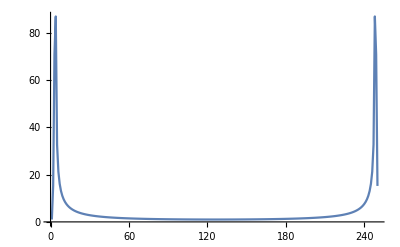

```mathematica
ListLinePlot[
Abs[stft["Data"][[4]]],PlotRange->All
]
```

О проблеме частоты сигнала и размера окна. Чем больше окно, тем лучше находим низкие частоты, чем меньше тем - хуже.  Аналогично с высокими

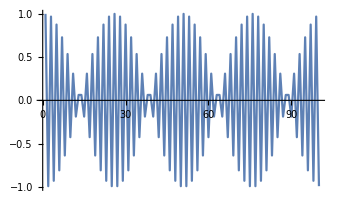

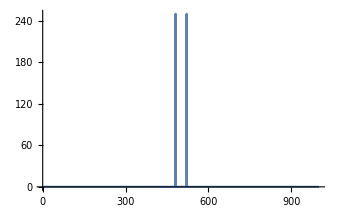

250.

{{480.}}

```mathematica
T=1;(* время в секундах *)
Δ=1000; (* колво отсчетов внутри T *)
sd[f_,T_,Δ_]:=Cos[ 2 Pi f T/Δ *t]
sig=Table[   sd[480,T,Δ], {t,0,Δ-1}];
ft= Abs[Fourier[sig]]^2;
ListLinePlot[sig[[;;100]],PlotRange->{-1,1}]
ListLinePlot[ft,PlotRange->All]
md=Max[   ft [[;;Δ/2 -1]] ]
max=Position[ft[[;;Δ/2 -1]] ,md];
f0=(#-1)/T &/@max //N
```

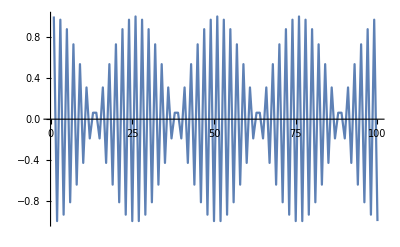

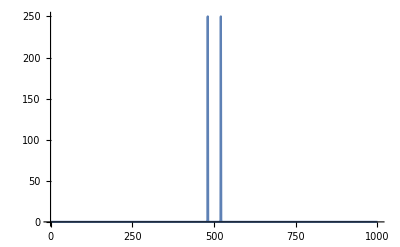

250.

{{480.}}

```mathematica
T=1;(* время в секундах *)
Δ=1000; (* колво отсчетов внутри T *)
sd[f_,T_,Δ_]:=Cos[ 2 Pi f T/Δ *t]
sig=Table[   sd[480,T,Δ], {t,0,Δ-1}];
ft= Abs[Fourier[sig]]^2;
ListLinePlot[sig[[;;100]],PlotRange->{-1,1}]
ListLinePlot[ft,PlotRange->All]
md=Max[   ft [[;;Δ/2 -1]] ]
max=Position[ft[[;;Δ/2 -1]] ,md];
f0=(#-1)/T &/@max //N
```

Таким образом, увеличивая временное окно, мы увеличиваем разрешение по времени и понижаем разращение по частоте сигнала, уменьшая окно - уменьшаем разрешение по времени и увеличиваем частотность сигнала. Это фундаментальная проблема Фурье преобразования связанная с базисной функцией (sin-cos)
Принцип неопределенности Гейзенберга. Этот принцип в применении к частотно-временному преобразованию гласит, что невозможно получить произвольно точное частотно-временное представление сигнала, то есть нельзя определить для какого-то момента времени, какие спектральные компоненты присутствуют в сигнале. Единственное, что мы можем знать, так это временные интервалы, в течение которых в сигнале существуют полосы частот. Эта проблема называется проблемой разрешения.

### Вейвлеты

Несмотря на то, что проблема разрешения имеет физический характер и не может быть преодолена, существует возможность анализа сигнала при помощи альтернативного подхода, имя которому - кратномасштабный анализ (КМА). КМА, как видно из названия, анализирует сигнал на различных частотах и различном разрешении одновременно. Каждая спектральная компонента не анализируется отдельно, как это было в случае с оконным преобразованием Фурье. КМА позволяет получить хорошее разрешение по времени (плохое по частоте) на высоких частотах и хорошее разрешение по частоте (плохое по времени) на низких частотах. Этот подход становится особенно эффективным, когда сигнал имеет высокочастотные компоненты короткой длительности и протяженные низкочастотные компоненты. К счастью, именно такие сигналы и встречаются чаще всего на практике.

Приведем пример масштабируемой функции:

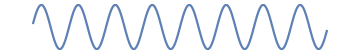
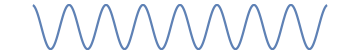
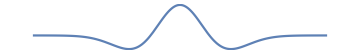
Sine | -Graphics-
Cosine | -Graphics-
Wavelet | -Graphics-

```mathematica
Grid[{{"Sine","Cosine","Wavelet"},
Plot[#,{x,-5,5},PlotRange->All,Axes->None,
AspectRatio->0.15, ImageSize->Medium]&/@{Sin[5x],Cos[5x],WaveletPsi[MexicanHatWavelet[],x]}
}//Transpose]
```

```mathematica
WaveletPsi[MexicanHatWavelet[],x]
```

-(2 ⅇ^(-x^2/2) (-1+x^2))/(√3 π^(1/4))

Допустимость. Материнский вейвлет ψ(t), должен иметь нулевое среднее значение

```mathematica
Integrate[   WaveletPsi[MexicanHatWavelet[],t],{t,-∞,+∞}]//N
```

0.

Подобие. Все функции семейства получаются из материнского вейвлета путем масштабного преобразования и сдвига

```mathematica
Manipulate[Plot[ WaveletPsi[MexicanHatWavelet[],(x-k)/s],
{x,-10,10},PlotRange->{-1,1},ImageSize->Medium],
{{s,2.5,"Масштаб"},1,5},{{k,0,"Сдвиг"},-5,5}]
```

(2 ⅇ^(-1/2 π^2 ω^2) π^(9/4) ω^2)/(√3)

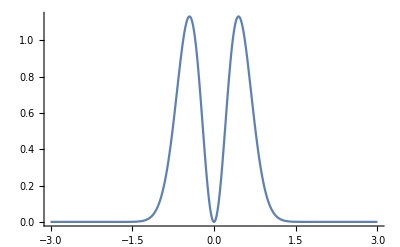

```mathematica
ft=FourierTransform[ WaveletPsi[MexicanHatWavelet[],x],x,ω,FourierParameters->{0,Pi}]//FullSimplify
Plot[ft,{ω,-3,3},PlotRange->All]
```

Для дискретных вейвлетов - масштабирующая функция

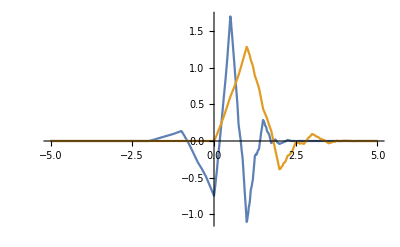

```mathematica
mother =  WaveletPsi[DaubechiesWavelet[3],t];
father =  WaveletPhi[DaubechiesWavelet[3],t];
Plot[{mother,father},{t,-5,5},PlotRange->All]
```

```mathematica
∫_(-∞)^∞ motherⅆt
∫_(-∞)^∞ fatherⅆt
```

3.2072×10^-17

1.

```mathematica
opts={ImageSize->500,Frame->True,ImagePadding->{{30,3},{15,3}}};
data=Table[Sign[Cos[x+Sin[x^2]]],{x,-6,6,0.025}];
cwt=ContinuousWaveletTransform[data];
Column[
{WaveletScalogram[cwt,ColorFunction->"SunsetColors",opts],
ListLinePlot[data,AspectRatio->1/4,opts],
ListLinePlot[{data,InverseContinuousWaveletTransform[cwt]},AspectRatio->1/4,opts]}]
```

-Graphics-

```mathematica
opts={ImageSize->500,Frame->True,ImagePadding->{{30,3},{15,3}}};
data=Table[Sign[Cos[x+Sin[x^2]]],{x,-6,6,0.025}];
cwt=ContinuousWaveletTransform[data,MorletWavelet[]];
Column[{WaveletScalogram[cwt,ColorFunction->"SunsetColors",opts],
ListLinePlot[data,AspectRatio->1/4,opts],
ListLinePlot[{data,InverseContinuousWaveletTransform[cwt]},AspectRatio->1/4,opts]}]
```

-Graphics-

-Graphics-

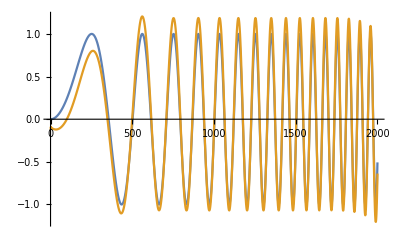

```mathematica
data = Table[Sin[100 t^2],{t,0,1,1./2000}];
cwt = ContinuousWaveletTransform[data];
WaveletScalogram[cwt]
ListLinePlot[{data,InverseContinuousWaveletTransform[cwt]}]
```

-Graphics-

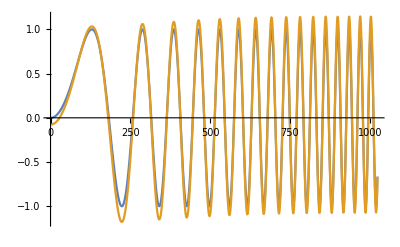

```mathematica
T=10;(* время в секундах *)
n=10;
Δ=2^n; (* колво отсчетов внутри T *)
st=Sin[t  (T/Δ)   *t  (T/Δ)];
xt=Table[st,{t,0,Δ-1}];
data=xt;
cwt = ContinuousWaveletTransform[data,MexicanHatWavelet[],{Automatic,16},Padding->0.0,SampleRate->2000];
WaveletScalogram[cwt]
ListLinePlot[{data,InverseContinuousWaveletTransform[cwt]}]
```

-Graphics-

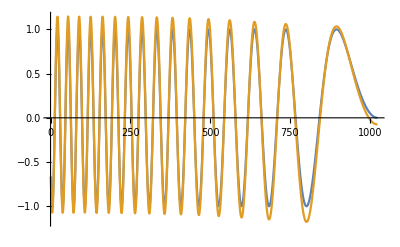

```mathematica
data=Reverse[xt];
cwt = ContinuousWaveletTransform[data,MexicanHatWavelet[],{Automatic,16},Padding->0.0,SampleRate->2000];
WaveletScalogram[cwt]
ListLinePlot[{data,InverseContinuousWaveletTransform[cwt]}]
```

-Graphics-

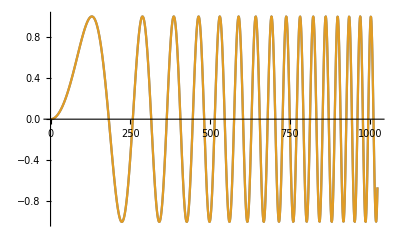

```mathematica
dwd=DiscreteWaveletTransform[xt,Automatic,9];
idwd=InverseWaveletTransform[dwd];
WaveletScalogram[dwd,Ticks->Full]
ListLinePlot[{xt,idwd}]
```

-Graphics-

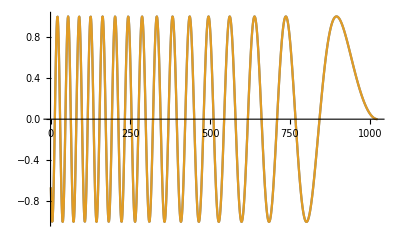

```mathematica
rxt=Reverse[xt];
dwd=DiscreteWaveletTransform[rxt,Automatic,9];
idwd=InverseWaveletTransform[dwd];
WaveletScalogram[dwd,Ticks->Full]
ListLinePlot[{rxt,idwd}]
```

DiscreteWaveletData[<<DWT>>, <9>, {1024}]

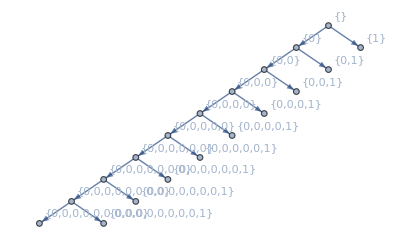

-Graphics-

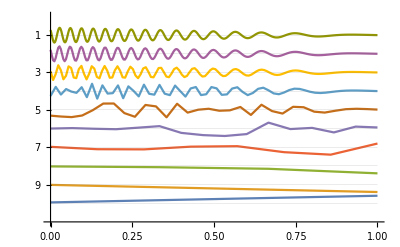

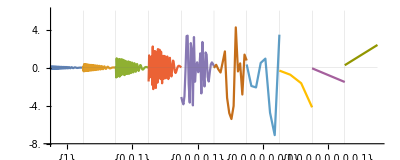

```mathematica
dwd=DiscreteWaveletTransform[rxt,Automatic,9]
dwd["TreeView"]
WaveletScalogram[dwd,Ticks->Full]
WaveletListPlot[dwd,FrameTicks->Full,DataRange->{0,1}]
WaveletListPlot[dwd,Ticks->Full,PlotLayout->"CommonYAxis"]
```

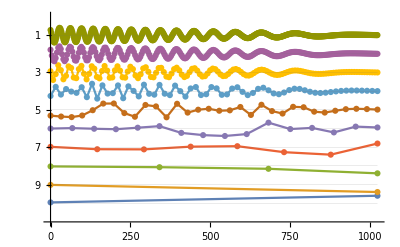

```mathematica
WaveletListPlot[dwd,PlotMarkers->Automatic]
```

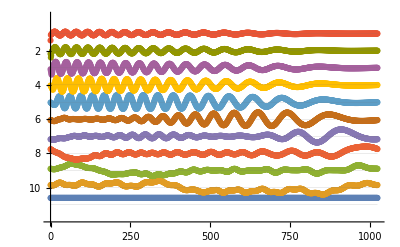

```mathematica
dwd=StationaryWaveletTransform[rxt];
WaveletListPlot[dwd,PlotMarkers->Automatic]
```

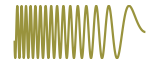
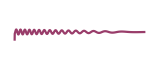
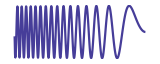
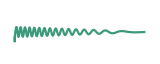
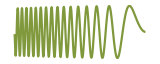
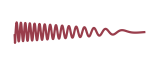
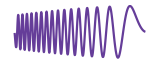
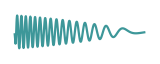
{{0}→-Graphics-,{1}→-Graphics-,{0,0}→-Graphics-,{0,1}→-Graphics-,{0,0,0}→-Graphics-,{0,0,1}→-Graphics-,{0,0,0,0}→-Graphics-,{0,0,0,1}→-Graphics-,{0,0,0,0,0}→-Graphics-,{0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0}→-Graphics-,{0,0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0,0}→-Graphics-,{0,0,0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0,0,0}→-Graphics-,{0,0,0,0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0,0,0,0}→-Graphics-,{0,0,0,0,0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0,0,0,0,0}→-Graphics-,{0,0,0,0,0,0,0,0,0,1}→-Graphics-}

```mathematica
dwd[All,{"ListPlot",ImageSize->160}]
```

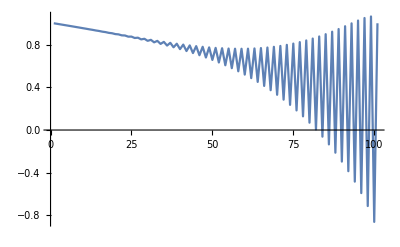

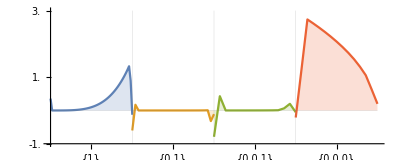

```mathematica
data=Table[n^4(-1)^(100n)+√(1-n),{n,0,1,0.01}];
ListLinePlot[data]
dwd=DiscreteWaveletTransform[data,DaubechiesWavelet[2],3,Padding->0];
WaveletListPlot[dwd,Ticks->Full,PlotLayout->"CommonYAxis",Filling->Axis]
```

## Фильтрация (шумоподавление)

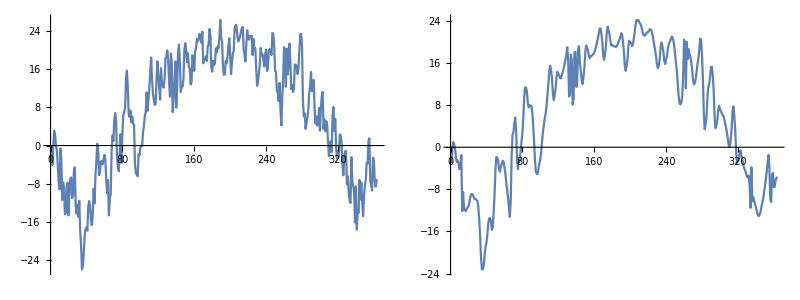

```mathematica
dataval=WeatherData["KMDZ","MeanTemperature",{{2007,1,1},{2007,12,31},"Day"}]["Values"];
dwdth=DiscreteWaveletTransform[dataval,DaubechiesWavelet[4],4];
thr=WaveletThreshold[dwdth];
Grid[{{ListLinePlot[dataval,ImageSize->300],ListLinePlot[InverseWaveletTransform[thr],ImageSize->300]}}]
```

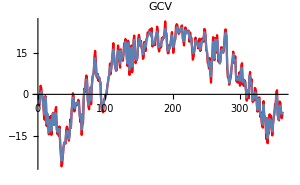
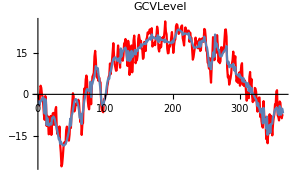
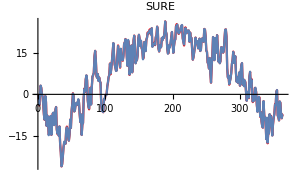
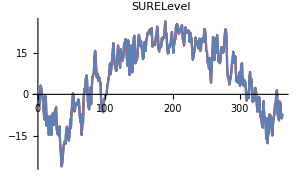
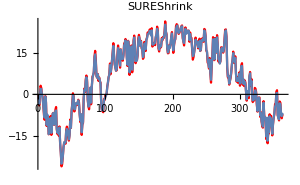
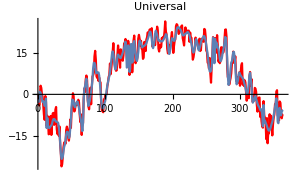
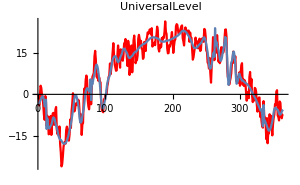
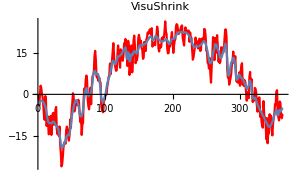

```mathematica
Table[
Show[
ListLinePlot[dataval,PlotStyle->Red,ImageSize->300,PlotLabel->tspec],
ListLinePlot[
InverseWaveletTransform[WaveletThreshold[dwdth,tspec]]
]
],{tspec,{"GCV","GCVLevel","SURE","SURELevel","SUREShrink","Universal","UniversalLevel","VisuShrink","VisuShrinkLevel"}}]
```

Wavelet Index | Threshold Value | 
{1} | 5.39208 | 
{0,1} | 5.89217 | 
{0,0,1} | 10.1358 | 
{0,0,0,1} | 15.6124 |

{1}→0.0102421
{0,1}→0.0167364
{0,0,1}→0.0259139
{0,0,0,1}→0.033486
{0,0,0,0}→0.913622

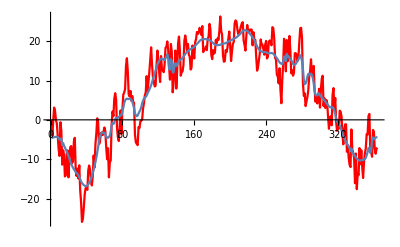

```mathematica
thr = WaveletThreshold[dwdth,{"Soft",Abs[FindThreshold[#,Method->"MinimumError"]]&}];
thr["ThresholdTable"]
dwdth["EnergyFraction"]//TableForm

Show[
ListLinePlot[dataval,PlotStyle->Red,ImageSize->400],
ListLinePlot[
InverseWaveletTransform[
thr
]
]]
```

## Пакетное преобразование

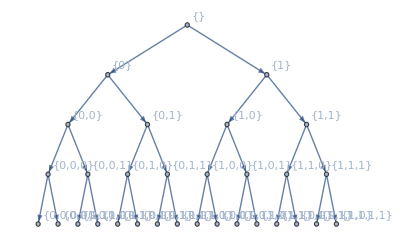

```mathematica
dat = dataval;
wavelet=DaubechiesWavelet[4];
dwd=StationaryWaveletPacketTransform[dat, wavelet,4];
dwd["TreeView"]
```

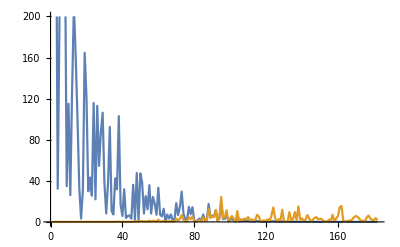

```mathematica
cof=dwd[{0}][[1,2]];
det=dwd[{1}][[1,2]];
cofF=Abs[Fourier[cof]]^2;
detF=Abs[Fourier[det]]^2;
ListLinePlot[{
cofF[[;;Round[Length[cofF]/2     ]  ]],
detF[[;;Round[Length[detF] /2    ]  ]]
 },PlotRange->{0,200}]
```

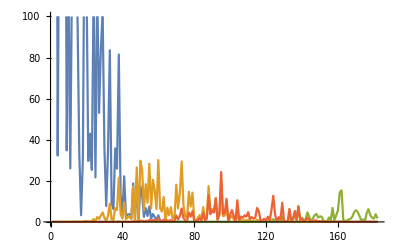

```mathematica
cof0=dwd[{0,0}][[1,2]];
det0=dwd[{0,1}][[1,2]];
cof1=dwd[{1,0}][[1,2]];
det1=dwd[{1,1}][[1,2]];
cof0=Abs[Fourier[cof0]]^2;
det0=Abs[Fourier[det0]]^2;
cof1=Abs[Fourier[cof1]]^2;
det1=Abs[Fourier[det1]]^2;
ListLinePlot[{
cof0[[;;Round[Length[cofF]/2     ]  ]],
det0[[;;Round[Length[detF] /2    ]  ]],
cof1[[;;Round[Length[cofF]/2     ]  ]],
det1[[;;Round[Length[detF] /2    ]  ]]
 },PlotRange->{0,100}]
```

DiscreteWaveletData[<<DWPT>>, <4>, {364}]

{{0,0,1},{1,0,0},{1,0,1},{1,1,1},{0,0,0,0},{0,0,0,1},{0,1,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,1,0,0},{1,1,0,1}}

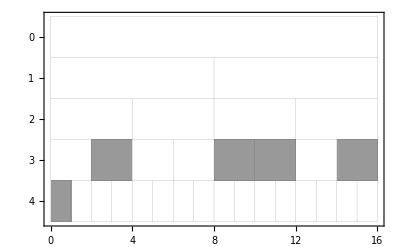

```mathematica
dwd=DiscreteWaveletPacketTransform[dat];
best=WaveletBestBasis[dwd]
WaveletBestBasis[dwd]["BasisIndex"]
WaveletBestBasis[dwd]["BestBasisBlockView"]
```

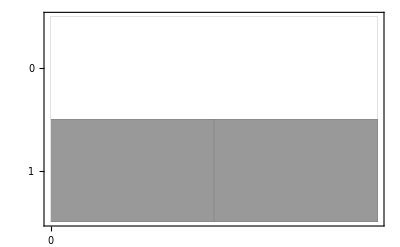
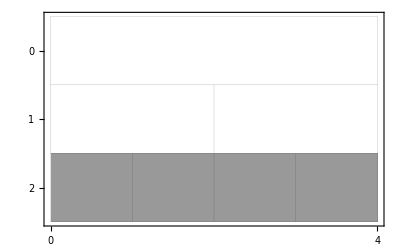
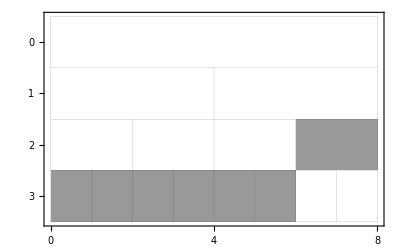
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[WaveletBestBasis[DiscreteWaveletPacketTransform[dat,Automatic,r]]["BestBasisBlockView"],{r,4}]
```

```mathematica
WaveletBestBasis[dwd]["BestBasisCostTable"]
```

Wavelet Index | Cost Values | Basis Index
{} | -410539. | ×
{0} | -450161. | ×
{1} | -3538.62 | ×
{0,0} | -487915. | ×
{0,1} | -4173.01 | ×
{1,0} | -1409.5 | ×
{1,1} | -2303.65 | ×
{0,0,0} | -520352. | ×
{0,0,1} | -7836.48 | ✓
{0,1,0} | -1797.75 | ×
{0,1,1} | -2412.27 | ×
{1,0,0} | -591.236 | ✓
{1,0,1} | -939.663 | ✓
{1,1,0} | -1317.45 | ×
{1,1,1} | -948.412 | ✓
{0,0,0,0} | -544585. | ✓
{0,0,0,1} | -12765.2 | ✓
{0,0,1,0} | -3649.94 | ×
{0,0,1,1} | -4043.95 | ×
{0,1,0,0} | -739.415 | ✓
{0,1,0,1} | -1111.61 | ✓
{0,1,1,0} | -1552.71 | ✓
{0,1,1,1} | -926.262 | ✓
{1,0,0,0} | -320.225 | ×
{1,0,0,1} | -191.581 | ×
{1,0,1,0} | -277.916 | ×
{1,0,1,1} | -629.322 | ×
{1,1,0,0} | -1191.81 | ✓
{1,1,0,1} | -270.928 | ✓
{1,1,1,0} | -436.901 | ×
{1,1,1,1} | -478.606 | ×